```mathematica
Integrate[-x Exp[-x],x]
```

-ⅇ^-x (-1-x)

```mathematica
Clear[ω]
```

```mathematica
D[Exp[-r^2/ω^2],r]
```

-(2 ⅇ^(-r^2/ω^2) r)/ω^2

```mathematica
ω??
```

Information::basic: ?Name gives information on Name, ?Ab* on all symbols starting with Ab. ??Name gives more information.

0.0002

```mathematica
Integrate[Exp[-r^2/ω^2]Exp[-r/a],{r,0,∞}]
```

ConditionalExpression[1/2 ⅇ^(ω^2/(4 a^2)) √π ω (-1+√(1/ω^2) ω+Erfc[ω/(2 a)]),Re[ω^2]>0||(Re[ω^2]≥0&&Re[a]>0)]

```mathematica
Integrate[(1-Exp[-(1+Cos[x])*a])/((1+Cos[x])*a),{x,0,π}]
```

ConditionalExpression[ⅇ^-a π (BesselI[0,a]+BesselI[1,a]),Re[a]>0]

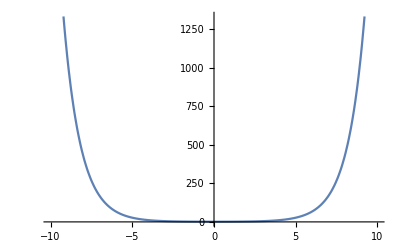

```mathematica
Plot[BesselI[0,x],{x,-10,10}]
```

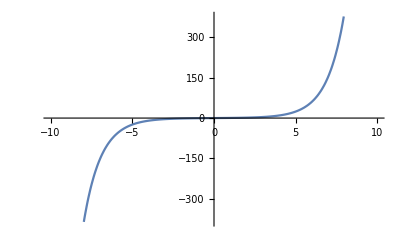

```mathematica
Plot[BesselI[1,x],{x,-10,10}]
```

Bessel function tests, plotting Bessel functions:

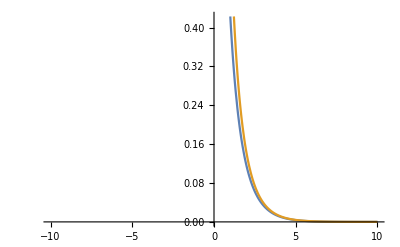

```mathematica
Plot[{BesselK[0,x],BesselK[1,x]},{x,-10,10}]
```

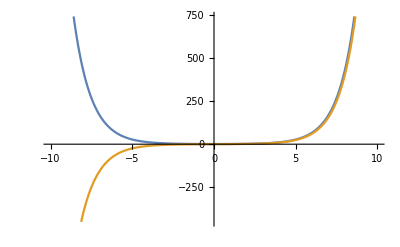

```mathematica
Plot[{BesselI[0,x],BesselI[1,x]},{x,-10,10}]
```

```mathematica
BesselK[0,1]
```

BesselK[0,1]

```mathematica
BesselK[1,1]
```

BesselK[1,1]

```mathematica
N[BesselK[1,11]]
```

6.52086×10^-6

```mathematica
N[BesselK[0,1]]
```

0.421024

```mathematica
BesselI[0,4.2]
```

13.4425

```mathematica
BesselJ[0,4.2 I]
```

13.4425+0. ⅈ

```mathematica
Table[BesselK[1,x],{x,0,25,0.1}]//TableForm
```

ComplexInfinity
9.85384
4.77597
3.05599
2.18435
1.65644
1.30283
1.05028
0.861782
0.716534
0.601907
0.50976
0.434592
0.372547
0.320836
0.277388
0.240634
0.209362
0.182623
0.15966
0.139866
0.122746
0.107897
0.0949824
0.0837248
0.0738908
0.065284
0.0577384
0.0511127
0.0452864
0.0401564
0.0356341
0.0316429
0.0281169
0.024999
0.0222394
0.019795
0.017628
0.0157057
0.0139993
0.0124835
0.0111363
0.0099382
0.00887221
0.00792325
0.00707809
0.00632504
0.00565378
0.00505518
0.00452117
0.00404461
0.00361918
0.00323926
0.00289988
0.00259663
0.00232557
0.00208322
0.0018665
0.00167263
0.00149916
0.00134392
0.00120495
0.00108053
0.000969109
0.000869306
0.000779894
0.000699778
0.000627977
0.000563617
0.000505918
0.000454182
0.000407786
0.000366172
0.000328842
0.00029535
0.000265297
0.000238327
0.000214121
0.000192392
0.000172884
0.000155369
0.000139641
0.000125516
0.00011283
0.000101434
0.0000911972
0.0000819997
0.0000737355
0.0000663093
0.0000596353
0.000053637
0.0000482454
0.0000433988
0.0000390417
0.0000351243
0.000031602
0.0000284348
0.0000255865
0.000023025
0.0000207211
0.0000186488
0.0000167847
0.0000151078
0.0000135991
0.0000122418
0.0000110205
9.92153×10^-6
8.93261×10^-6
8.04266×10^-6
7.24173×10^-6
6.52086×10^-6
5.87202×10^-6
5.28799×10^-6
4.76225×10^-6
4.28897×10^-6
3.86289×10^-6
3.47929×10^-6
3.13391×10^-6
2.82293×10^-6
2.54291×10^-6
2.29076×10^-6
2.06369×10^-6
1.8592×10^-6
1.67503×10^-6
1.50916×10^-6
1.35977×10^-6
1.22521×10^-6
1.104×10^-6
9.94817×10^-7
8.96462×10^-7
8.07859×10^-7
7.28036×10^-7
6.56122×10^-7
5.9133×10^-7
5.32953×10^-7
4.80354×10^-7
4.32958×10^-7
3.90251×10^-7
3.51767×10^-7
3.17087×10^-7
2.85834×10^-7
2.57669×10^-7
2.32286×10^-7
2.09408×10^-7
1.88789×10^-7
1.70205×10^-7
1.53454×10^-7
1.38355×10^-7
1.24745×10^-7
1.12477×10^-7
1.01417×10^-7
9.14476×10^-8
8.24599×10^-8
7.43573×10^-8
6.70524×10^-8
6.04666×10^-8
5.45288×10^-8
4.91753×10^-8
4.43483×10^-8
3.9996×10^-8
3.60716×10^-8
3.25329×10^-8
2.9342×10^-8
2.64647×10^-8
2.38699×10^-8
2.153×10^-8
1.94199×10^-8
1.75169×10^-8
1.58007×10^-8
1.4253×10^-8
1.2857×10^-8
1.15981×10^-8
1.04625×10^-8
9.43837×10^-9
8.51461×10^-9
7.6814×10^-9
6.92984×10^-9
6.25193×10^-9
5.64043×10^-9
5.08883×10^-9
4.59125×10^-9
4.14239×10^-9
3.73747×10^-9
3.37219×10^-9
3.04266×10^-9
2.74538×10^-9
2.47718×10^-9
2.23521×10^-9
2.01691×10^-9
1.81996×10^-9
1.64227×10^-9
1.48194×10^-9
1.33729×10^-9
1.20678×10^-9
1.08901×10^-9
9.82759×10^-10
8.86883×10^-10
8.00371×10^-10
7.22309×10^-10
6.51869×10^-10
5.88306×10^-10
5.30948×10^-10
4.79189×10^-10
4.32481×10^-10
3.90331×10^-10
3.52293×10^-10
3.17967×10^-10
2.86988×10^-10
2.59031×10^-10
2.338×10^-10
2.1103×10^-10
1.90479×10^-10
1.71932×10^-10
1.55193×10^-10
1.40085×10^-10
1.26449×10^-10
1.14142×10^-10
1.03034×10^-10
9.30075×10^-11
8.3958×10^-11
7.57898×10^-11
6.84171×10^-11
6.17622×10^-11
5.57553×10^-11
5.03331×10^-11
4.54387×10^-11
4.10207×10^-11
3.70326×10^-11
3.34326×10^-11
3.01829×10^-11
2.72493×10^-11
2.46011×10^-11
2.22105×10^-11
2.00524×10^-11
1.81041×10^-11
1.63453×10^-11
1.47575×10^-11
1.33241×10^-11
1.203×10^-11
1.08617×10^-11
9.807×10^-12
8.85476×10^-12
7.99505×10^-12
7.21888×10^-12
6.51812×10^-12
5.88543×10^-12
5.31421×10^-12
4.79846×10^-12
4.33281×10^-12
3.91238×10^-12
3.53278×10^-12

```mathematica
Table[BesselK[0,x],{x,0,25,0.1}] // TableForm
```

∞
2.42707
1.7527
1.37246
1.11453
0.924419
0.777522
0.66052
0.565347
0.48673
0.421024
0.365602
0.318508
0.278248
0.243655
0.213806
0.187955
0.165496
0.145931
0.128846
0.113894
0.100784
0.089269
0.0791399
0.0702173
0.0623476
0.0553983
0.0492554
0.04382
0.0390062
0.0347395
0.0309547
0.027595
0.0246106
0.021958
0.0195989
0.0174996
0.0156307
0.0139659
0.0124823
0.0111597
0.00998001
0.00892745
0.00798797
0.00714911
0.00639986
0.00573042
0.00513212
0.00459725
0.00411894
0.0036911
0.00330831
0.00296575
0.00265911
0.00238457
0.00213871
0.00191849
0.00172121
0.00154443
0.00138601
0.00124399
0.00111668
0.00100252
0.000900139
0.00080831
0.000725932
0.000652021
0.000585699
0.000526178
0.000472754
0.000424796
0.000381739
0.000343079
0.000308362
0.000277183
0.000249178
0.000224021
0.00020142
0.000181114
0.000162868
0.000146471
0.000131734
0.000118489
0.000106583
0.00009588
0.0000862576
0.0000776059
0.0000698265
0.0000628309
0.0000565396
0.0000508813
0.000045792
0.0000412141
0.0000370959
0.0000333911
0.0000300579
0.0000270588
0.0000243603
0.000021932
0.0000197467
0.0000177801
0.00001601
0.0000144169
0.0000129829
0.000011692
0.00001053
9.48385×10^-6
8.54202×10^-6
7.69403×10^-6
6.93052×10^-6
6.24302×10^-6
5.62395×10^-6
5.06646×10^-6
4.56441×10^-6
4.11226×10^-6
3.70504×10^-6
3.33826×10^-6
3.00791×10^-6
2.71034×10^-6
2.44229×10^-6
2.20083×10^-6
1.9833×10^-6
1.78734×10^-6
1.61078×10^-6
1.45172×10^-6
1.3084×10^-6
1.17927×10^-6
1.06292×10^-6
9.58072×10^-7
8.63593×10^-7
7.78454×10^-7
7.01729×10^-7
6.32584×10^-7
5.70267×10^-7
5.14104×10^-7
4.63484×10^-7
4.1786×10^-7
3.76736×10^-7
3.39669×10^-7
3.06256×10^-7
2.76137×10^-7
2.48986×10^-7
2.24511×10^-7
2.02446×10^-7
1.82554×10^-7
1.6462×10^-7
1.48452×10^-7
1.33874×10^-7
1.20731×10^-7
1.08881×10^-7
9.81954×10^-8
8.85607×10^-8
7.98731×10^-8
7.20393×10^-8
6.49751×10^-8
5.86048×10^-8
5.28602×10^-8
4.76796×10^-8
4.30076×10^-8
3.87941×10^-8
3.49941×10^-8
3.15669×10^-8
2.84759×10^-8
2.56881×10^-8
2.31736×10^-8
2.09056×10^-8
1.88599×10^-8
1.70147×10^-8
1.53503×10^-8
1.3849×10^-8
1.24947×10^-8
1.1273×10^-8
1.01709×10^-8
9.17677×10^-9
8.27992×10^-9
7.47084×10^-9
6.74092×10^-9
6.08241×10^-9
5.48832×10^-9
4.95233×10^-9
4.46875×10^-9
4.03246×10^-9
3.63881×10^-9
3.28364×10^-9
2.96318×10^-9
2.67403×10^-9
2.41314×10^-9
2.17772×10^-9
1.96531×10^-9
1.77363×10^-9
1.60067×10^-9
1.4446×10^-9
1.30376×10^-9
1.17667×10^-9
1.06198×10^-9
9.58482×10^-10
8.65082×10^-10
7.80794×10^-10
7.04727×10^-10
6.36078×10^-10
5.74124×10^-10
5.1821×10^-10
4.67748×10^-10
4.22204×10^-10
3.811×10^-10
3.44001×10^-10
3.10517×10^-10
2.80296×10^-10
2.53019×10^-10
2.28399×10^-10
2.06177×10^-10
1.86119×10^-10
1.68014×10^-10
1.51672×10^-10
1.36921×10^-10
1.23606×10^-10
1.11587×10^-10
1.00738×10^-10
9.09445×10^-11
8.21039×10^-11
7.41235×10^-11
6.69195×10^-11
6.04162×10^-11
5.45454×10^-11
4.92456×10^-11
4.44612×10^-11
4.0142×10^-11
3.62428×10^-11
3.27226×10^-11
2.95446×10^-11
2.66755×10^-11
2.40852×10^-11
2.17466×10^-11
1.96353×10^-11
1.77292×10^-11
1.60082×10^-11
1.44544×10^-11
1.30516×10^-11
1.1785×10^-11
1.06414×10^-11
9.60882×10^-12
8.67654×10^-12
7.83478×10^-12
7.07475×10^-12
6.38849×10^-12
5.76886×10^-12
5.20936×10^-12
4.70417×10^-12
4.248×10^-12
3.8361×10^-12
3.46416×10^-12